```mathematica
sSphere[{x_,y_,z_},r_,color1_,color2_]:=Graphics3D[ParametricPlot3D[{x,y,z}+r {Cos[v] Cos[u],Cos[v] Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->15,MeshShading->{color1,color2},MeshStyle->Transparent,MeshFunctions->{#4&}][[1]]][[1]];
```

```mathematica
idxSamePhase1=DeleteDuplicates[Table[{idxSameDtO1t[[1,i]],Flatten@Select[Delete[idxSameDtO1t[[1]],{i}],Norm[Norm[Partition[flux[tU1[[2]],pars0,tU1[[1]]][0],3][[#]]&/@(idxSameDtO1t[[1,i]])]-
Norm[Partition[flux[tU1[[2]],pars0,tU1[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO1t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP1=idxSamePhase1[[All,1]][[All,1]];
```

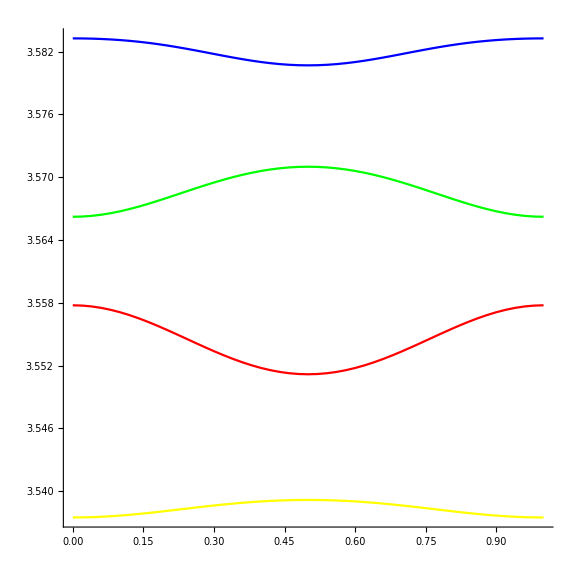

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU1[[2]],pars0,tU1[[1]]][t][[;;180]],3][[#]]&/@idxSP1),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP1]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU1[[2]],pars0,tU1[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase1[[i]])),
{i,Length@idxSP1}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU1[[2]],pars0,tU1[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase2=DeleteDuplicates[Table[{idxSameDtO2t[[1,i]],Flatten@Select[Delete[idxSameDtO2t[[1]],{i}],Norm[Norm[Partition[flux[tU2[[2]],pars0,tU2[[1]]][0],3][[#]]&/@(idxSameDtO2t[[1,i]])]-
Norm[Partition[flux[tU2[[2]],pars0,tU2[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO2t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP2=idxSamePhase2[[All,1]][[All,1]];
```

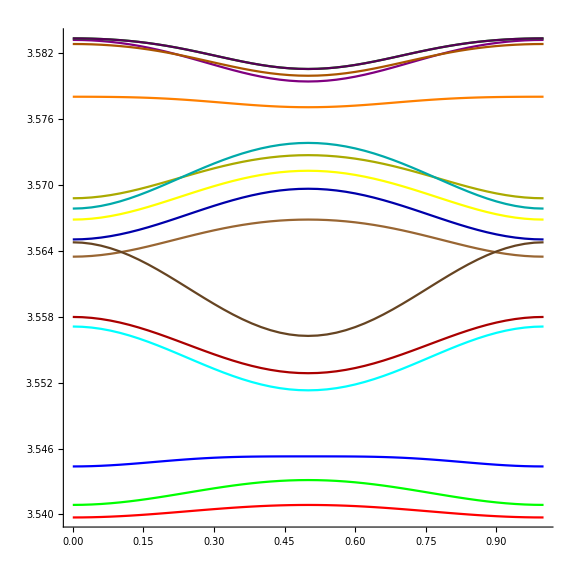

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU2[[2]],pars0,tU2[[1]]][t][[;;180]],3][[#]]&/@idxSP2),{t,0,1,0.02}],PlotStyle->colorSet2[[;;Length@idxSP2]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet2[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet2[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet2[[i]],White]}&,#]
]&@
(Partition[flux[tU2[[2]],pars0,tU2[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase2[[i]])),
{i,Length@idxSP2}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU2[[2]],pars0,tU2[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase3=DeleteDuplicates[Table[{idxSameDtO3t[[1,i]],Flatten@Select[Delete[idxSameDtO3t[[1]],{i}],Norm[Norm[Partition[flux[tU3[[2]],pars0,tU3[[1]]][0],3][[#]]&/@(idxSameDtO3t[[1,i]])]-
Norm[Partition[flux[tU3[[2]],pars0,tU3[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO3t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP3=idxSamePhase3[[All,1]][[All,1]];
```

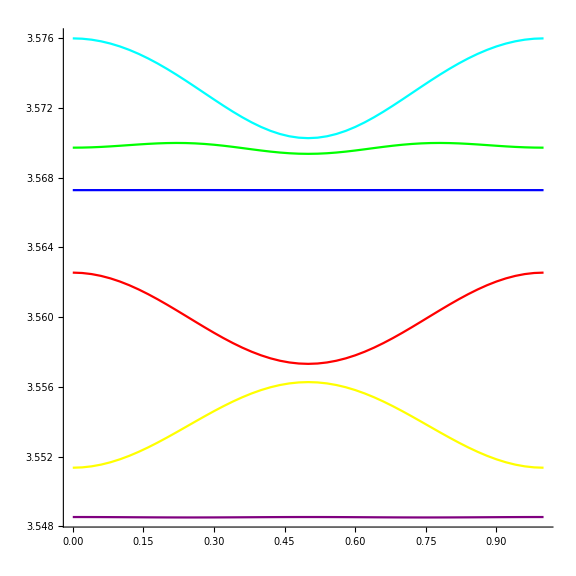

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU3[[2]],pars0,tU3[[1]]][t][[;;180]],3][[#]]&/@idxSP3),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP3]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU3[[2]],pars0,tU3[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase3[[i]])),
{i,Length@idxSP3}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU3[[2]],pars0,tU3[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase4=DeleteDuplicates[Table[{idxSameDtO4t[[1,i]],Flatten@Select[Delete[idxSameDtO4t[[1]],{i}],Norm[Norm[Partition[flux[tU4[[2]],pars0,tU4[[1]]][0],3][[#]]&/@(idxSameDtO4t[[1,i]])]-
Norm[Partition[flux[tU4[[2]],pars0,tU4[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO4t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP4=idxSamePhase4[[All,1]][[All,1]];
```

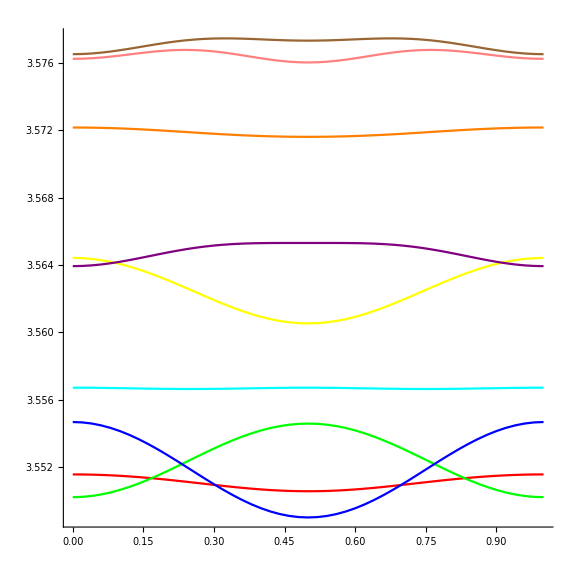

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU4[[2]],pars0,tU4[[1]]][t][[;;180]],3][[#]]&/@idxSP4),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP4]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU4[[2]],pars0,tU4[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase4[[i]])),
{i,Length@idxSP4}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU4[[2]],pars0,tU4[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase5=DeleteDuplicates[Table[{idxSameDtO5t[[1,i]],Flatten@Select[Delete[idxSameDtO5t[[1]],{i}],Norm[Norm[Partition[flux[tU5[[2]],pars0,tU5[[1]]][0],3][[#]]&/@(idxSameDtO5t[[1,i]])]-
Norm[Partition[flux[tU5[[2]],pars0,tU5[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO5t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP5=idxSamePhase5[[All,1]][[All,1]];
```

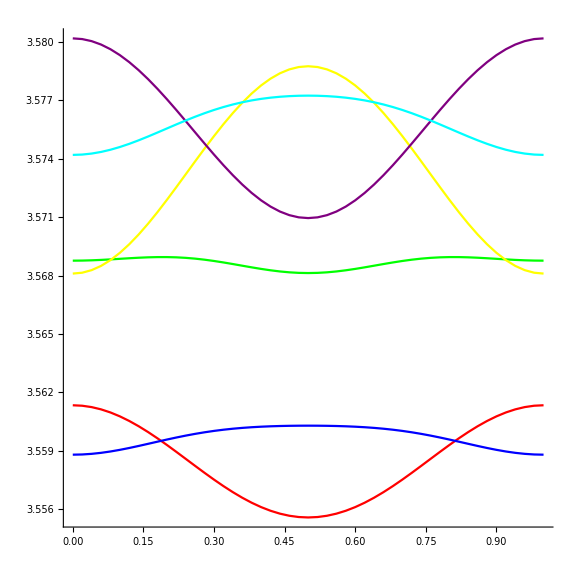

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU5[[2]],pars0,tU5[[1]]][t][[;;180]],3][[#]]&/@idxSP5),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP5]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU5[[2]],pars0,tU5[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase5[[i]])),
{i,Length@idxSP5}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU5[[2]],pars0,tU5[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase6=DeleteDuplicates[Table[{idxSameDtO6t[[1,i]],Flatten@Select[Delete[idxSameDtO6t[[1]],{i}],Norm[Norm[Partition[flux[tU6[[2]],pars0,tU6[[1]]][0],3][[#]]&/@(idxSameDtO6t[[1,i]])]-
Norm[Partition[flux[tU6[[2]],pars0,tU6[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO6t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP6=idxSamePhase6[[All,1]][[All,1]];
```

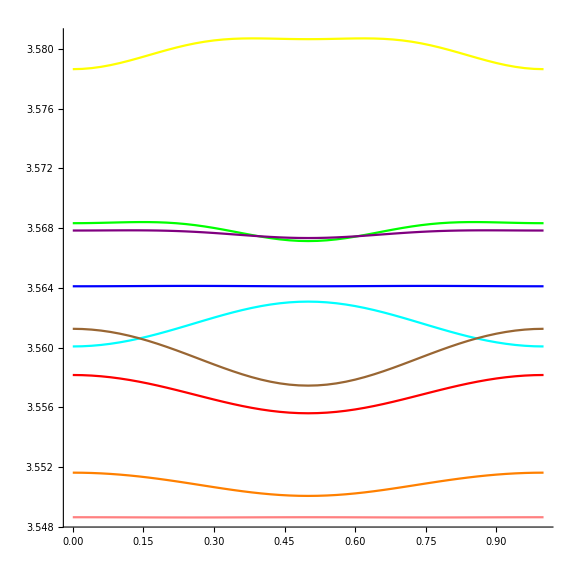

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU6[[2]],pars0,tU6[[1]]][t][[;;180]],3][[#]]&/@idxSP6),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP6]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU6[[2]],pars0,tU6[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase6[[i]])),
{i,Length@idxSP6}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU6[[2]],pars0,tU6[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase7=DeleteDuplicates[Table[{idxSameDtO7t[[1,i]],Flatten@Select[Delete[idxSameDtO7t[[1]],{i}],Norm[Norm[Partition[flux[tU7[[2]],pars0,tU7[[1]]][0],3][[#]]&/@(idxSameDtO7t[[1,i]])]-
Norm[Partition[flux[tU7[[2]],pars0,tU7[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO7t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP7=idxSamePhase7[[All,1]][[All,1]];
```

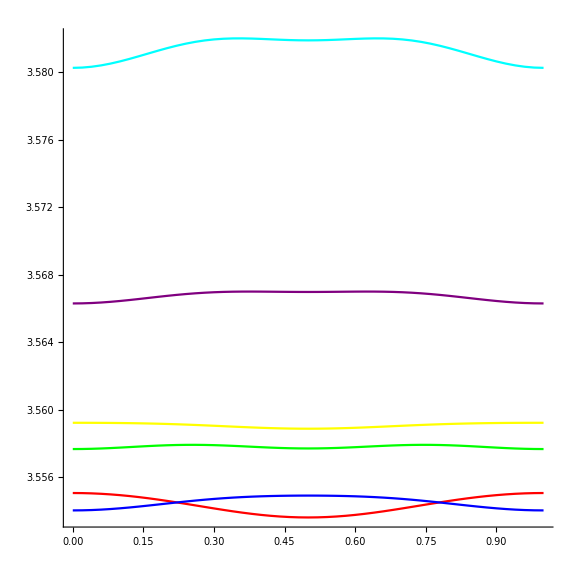

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU7[[2]],pars0,tU7[[1]]][t][[;;180]],3][[#]]&/@idxSP7),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP7]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU7[[2]],pars0,tU7[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase7[[i]])),
{i,Length@idxSP7}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU7[[2]],pars0,tU7[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase8=DeleteDuplicates[Table[{idxSameDtO8t[[1,i]],Flatten@Select[Delete[idxSameDtO8t[[1]],{i}],Norm[Norm[Partition[flux[tU8[[2]],pars0,tU8[[1]]][0],3][[#]]&/@(idxSameDtO8t[[1,i]])]-
Norm[Partition[flux[tU8[[2]],pars0,tU8[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO8t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP8=idxSamePhase8[[All,1]][[All,1]];
```

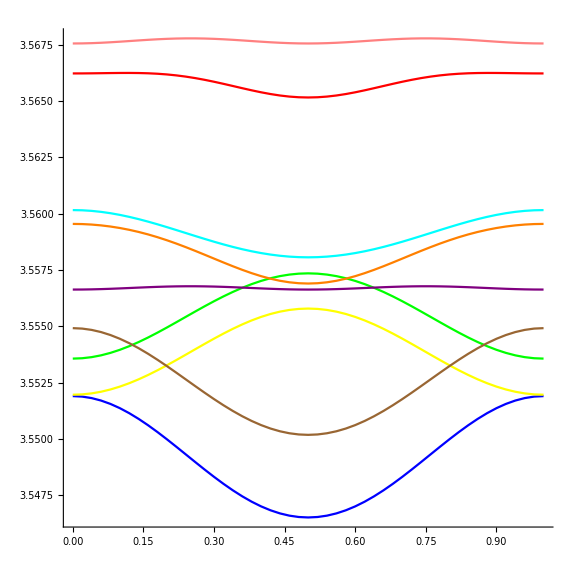

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU8[[2]],pars0,tU8[[1]]][t][[;;180]],3][[#]]&/@idxSP8),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP8]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU8[[2]],pars0,tU8[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase8[[i]])),
{i,Length@idxSP8}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU8[[2]],pars0,tU8[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase9=DeleteDuplicates[Table[{idxSameDtO9t[[1,i]],Flatten@Select[Delete[idxSameDtO9t[[1]],{i}],Norm[Norm[Partition[flux[tU9[[2]],pars0,tU9[[1]]][0],3][[#]]&/@(idxSameDtO9t[[1,i]])]-
Norm[Partition[flux[tU9[[2]],pars0,tU9[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO9t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP9=idxSamePhase9[[All,1]][[All,1]];
```

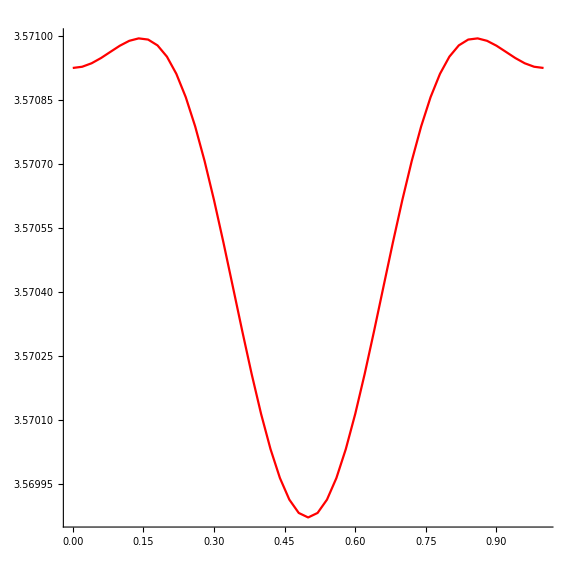

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU9[[2]],pars0,tU9[[1]]][t][[;;180]],3][[#]]&/@idxSP9),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP9]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU9[[2]],pars0,tU9[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase9[[i]])),
{i,Length@idxSP9}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU9[[2]],pars0,tU9[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase10=DeleteDuplicates[Table[{idxSameDtO10t[[1,i]],Flatten@Select[Delete[idxSameDtO10t[[1]],{i}],Norm[Norm[Partition[flux[tU10[[2]],pars0,tU10[[1]]][0],3][[#]]&/@(idxSameDtO10t[[1,i]])]-
Norm[Partition[flux[tU10[[2]],pars0,tU10[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO10t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP10=idxSamePhase10[[All,1]][[All,1]];
```

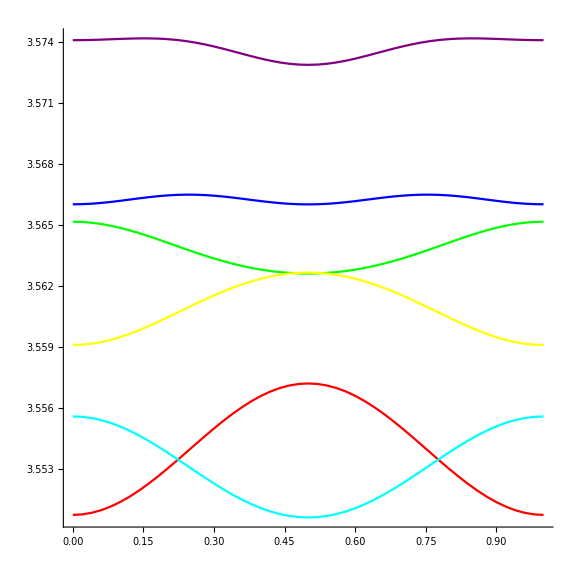

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU10[[2]],pars0,tU10[[1]]][t][[;;180]],3][[#]]&/@idxSP10),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP10]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU10[[2]],pars0,tU10[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase10[[i]])),
{i,Length@idxSP10}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU10[[2]],pars0,tU10[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase11=DeleteDuplicates[Table[{idxSameDtO11t[[1,i]],Flatten@Select[Delete[idxSameDtO11t[[1]],{i}],Norm[Norm[Partition[flux[tU11[[2]],pars0,tU11[[1]]][0],3][[#]]&/@(idxSameDtO11t[[1,i]])]-
Norm[Partition[flux[tU11[[2]],pars0,tU11[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO11t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP11=idxSamePhase11[[All,1]][[All,1]];
```

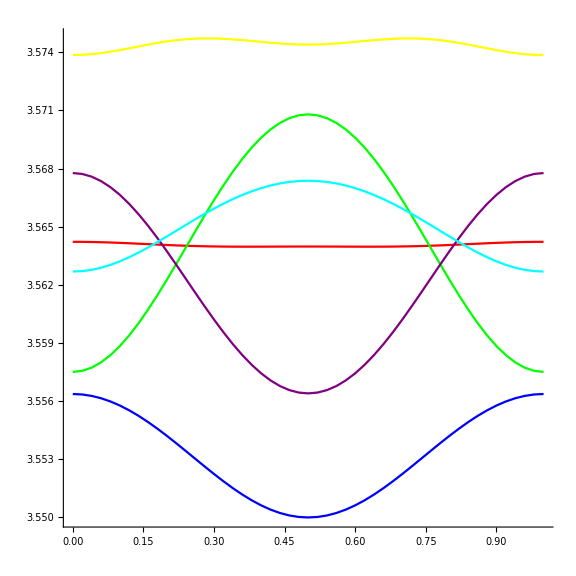

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU11[[2]],pars0,tU11[[1]]][t][[;;180]],3][[#]]&/@idxSP11),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP11]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU11[[2]],pars0,tU11[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase11[[i]])),
{i,Length@idxSP11}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU11[[2]],pars0,tU11[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase12=DeleteDuplicates[Table[{idxSameDtO12t[[1,i]],Flatten@Select[Delete[idxSameDtO12t[[1]],{i}],Norm[Norm[Partition[flux[tU12[[2]],pars0,tU12[[1]]][0],3][[#]]&/@(idxSameDtO12t[[1,i]])]-
Norm[Partition[flux[tU12[[2]],pars0,tU12[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO12t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP12=idxSamePhase12[[All,1]][[All,1]];
```

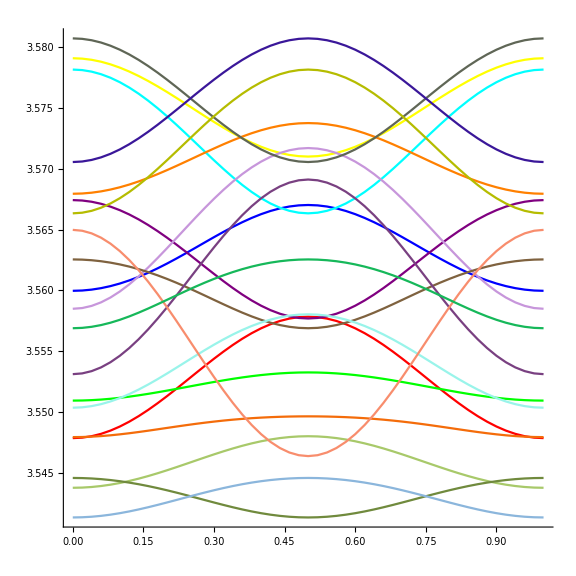

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU12[[2]],pars0,tU12[[1]]][t][[;;180]],3][[#]]&/@idxSP12),{t,0,1,0.02}],PlotStyle->colorSet12[[;;Length@idxSP12]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet12[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet12[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet12[[i]],White]}&,#]
]&@
(Partition[flux[tU12[[2]],pars0,tU12[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase12[[i]])),
{i,Length@idxSP12}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU12[[2]],pars0,tU12[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase13=DeleteDuplicates[Table[{idxSameDtO13t[[1,i]],Flatten@Select[Delete[idxSameDtO13t[[1]],{i}],Norm[Norm[Partition[flux[tU13[[2]],pars0,tU13[[1]]][0],3][[#]]&/@(idxSameDtO13t[[1,i]])]-
Norm[Partition[flux[tU13[[2]],pars0,tU13[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO13t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP13=idxSamePhase13[[All,1]][[All,1]];
```

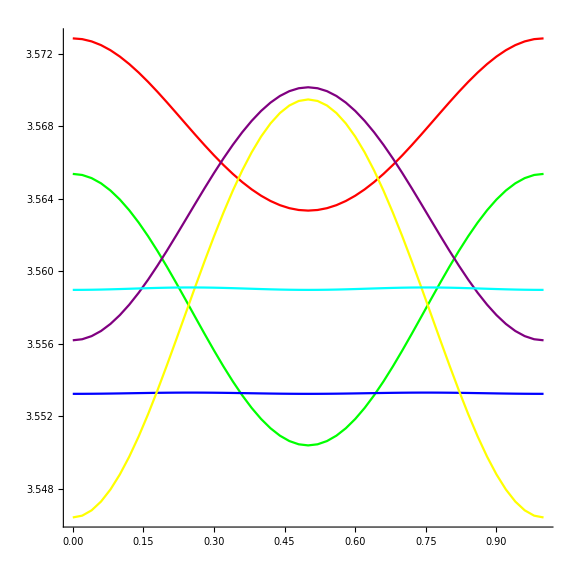

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU13[[2]],pars0,tU13[[1]]][t][[;;180]],3][[#]]&/@idxSP13),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP13]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU13[[2]],pars0,tU13[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase13[[i]])),
{i,Length@idxSP13}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU13[[2]],pars0,tU13[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase14=DeleteDuplicates[Table[{idxSameDtO14t[[1,i]],Flatten@Select[Delete[idxSameDtO14t[[1]],{i}],Norm[Norm[Partition[flux[tU14[[2]],pars0,tU14[[1]]][0],3][[#]]&/@(idxSameDtO14t[[1,i]])]-
Norm[Partition[flux[tU14[[2]],pars0,tU14[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO14t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP14=idxSamePhase14[[All,1]][[All,1]];
```

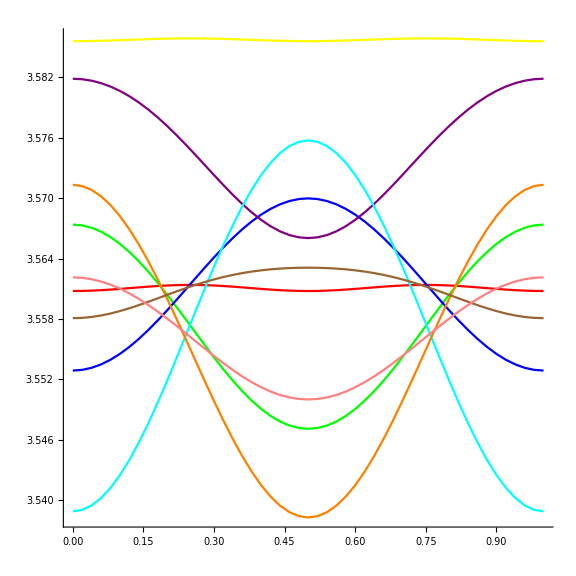

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU14[[2]],pars0,tU14[[1]]][t][[;;180]],3][[#]]&/@idxSP14),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP14]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU14[[2]],pars0,tU14[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase14[[i]])),
{i,Length@idxSP14}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU14[[2]],pars0,tU14[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase15=DeleteDuplicates[Table[{idxSameDtO15t[[1,i]],Flatten@Select[Delete[idxSameDtO15t[[1]],{i}],Norm[Norm[Partition[flux[tU15[[2]],pars0,tU15[[1]]][0],3][[#]]&/@(idxSameDtO15t[[1,i]])]-
Norm[Partition[flux[tU15[[2]],pars0,tU15[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO15t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP15=idxSamePhase15[[All,1]][[All,1]];
```

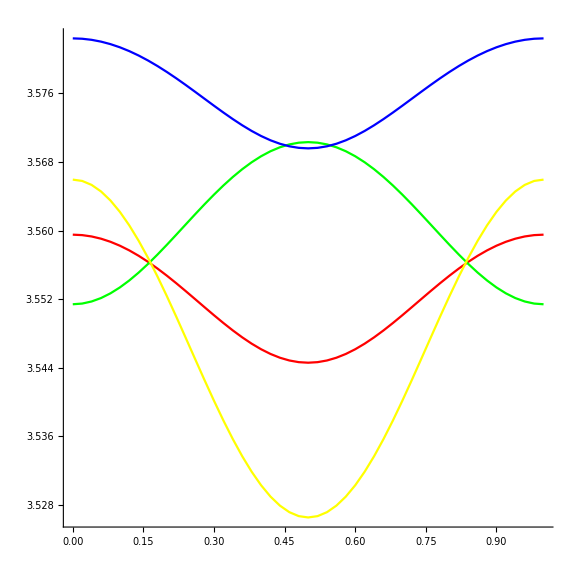

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU15[[2]],pars0,tU15[[1]]][t][[;;180]],3][[#]]&/@idxSP15),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP15]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU15[[2]],pars0,tU15[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase15[[i]])),
{i,Length@idxSP15}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU15[[2]],pars0,tU15[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase20=DeleteDuplicates[Table[{idxSameDtO20t[[1,i]],Flatten@Select[Delete[idxSameDtO20t[[1]],{i}],Norm[Norm[Partition[flux[tU20[[2]],pars0,tU20[[1]]][0],3][[#]]&/@(idxSameDtO20t[[1,i]])]-
Norm[Partition[flux[tU20[[2]],pars0,tU20[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO20t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP20=idxSamePhase20[[All,1]][[All,1]];
```

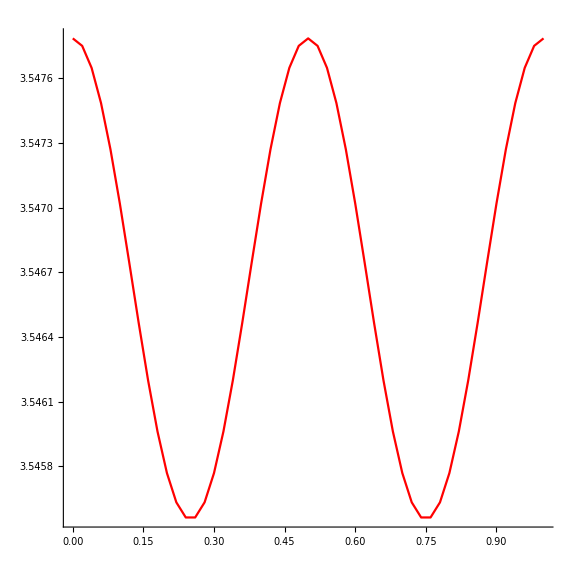

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU20[[2]],pars0,tU20[[1]]][t][[;;180]],3][[#]]&/@idxSP20),{t,0,1,0.02}],PlotStyle->colorSet3[[;;Length@idxSP20]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3[[i]],White]}&,#]
]&@
(Partition[flux[tU20[[2]],pars0,tU20[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase20[[i]])),
{i,Length@idxSP20}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU20[[2]],pars0,tU20[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase3S4=DeleteDuplicates[Table[{idxSameDtO3S4t[[1,i]],Flatten@Select[Delete[idxSameDtO3S4t[[1]],{i}],Norm[Norm[Partition[flux[tU3S4[[2]],pars0,tU3S4[[1]]][0],3][[#]]&/@(idxSameDtO3S4t[[1,i]])]-
Norm[Partition[flux[tU3S4[[2]],pars0,tU3S4[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO3S4t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP3S4=idxSamePhase3S4[[All,1]][[All,1]];
```

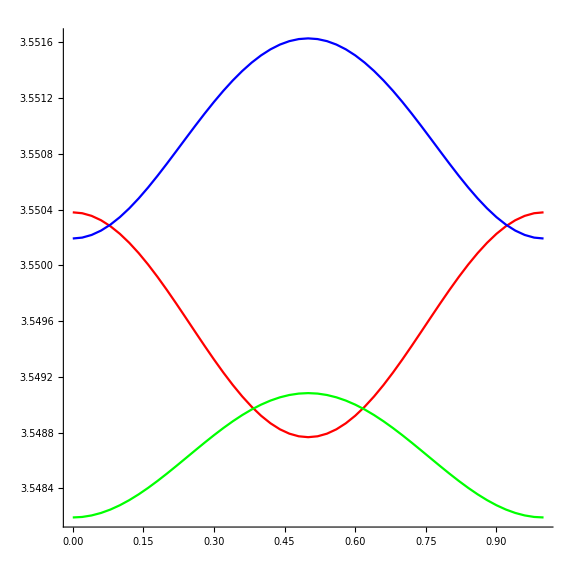

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU3S4[[2]],pars0,tU3S4[[1]]][t][[;;180]],3][[#]]&/@idxSP3S4),{t,0,1,0.02}],PlotStyle->colorSet3S4[[;;Length@idxSP3S4]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3S4[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3S4[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3S4[[i]],White]}&,#]
]&@
(Partition[flux[tU3S4[[2]],pars0,tU3S4[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase3S4[[i]])),
{i,Length@idxSP3S4}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU3S4[[2]],pars0,tU3S4[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```

```mathematica
idxSamePhase3S42=DeleteDuplicates[Table[{idxSameDtO3S42t[[1,i]],Flatten@Select[Delete[idxSameDtO3S42t[[1]],{i}],Norm[Norm[Partition[flux[tU3S42[[2]],pars0,tU3S42[[1]]][0],3][[#]]&/@(idxSameDtO3S42t[[1,i]])]-
Norm[Partition[flux[tU3S42[[2]],pars0,tU3S42[[1]]][0.5],3][[#]]&/@(#)]]<10^-6&]},{i,Length@idxSameDtO3S42t[[1]]}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
idxSP3S42=idxSamePhase3S42[[All,1]][[All,1]];
```

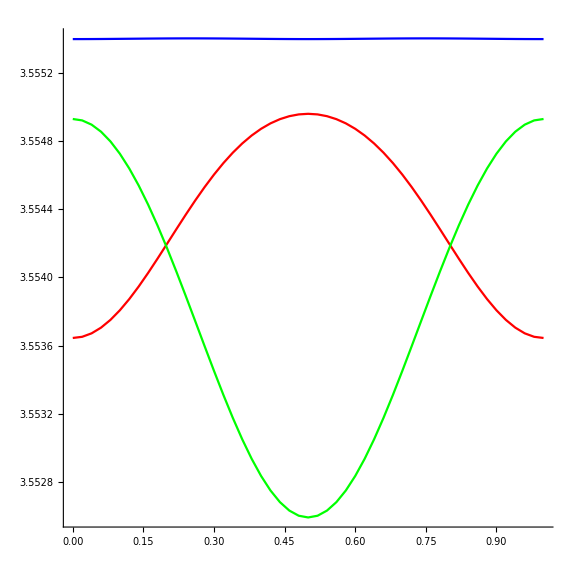

```mathematica
GraphicsRow[{
ListLinePlot[Transpose@Table[{t,#}&/@(Norm@Partition[flux[tU3S42[[2]],pars0,tU3S42[[1]]][t][[;;180]],3][[#]]&/@idxSP3S42),{t,0,1,0.02}],PlotStyle->colorSet3S42[[;;Length@idxSP3S42]],ImageSize->Large,AspectRatio->1],
Graphics3D[{
Table[
If[#[[2]]=={},
{colorSet3S42[[i]],Sphere[#[[1]],0.15]},
MapThread[{{colorSet3S42[[i]],Sphere[#1,0.15]},sSphere[#2,0.15,colorSet3S42[[i]],White]}&,#]
]&@
(Partition[flux[tU3S42[[2]],pars0,tU3S42[[1]]][0][[;;180]],3][[#]]&/@(idxSamePhase3S42[[i]])),
{i,Length@idxSP3S42}],
{Gray,Cylinder[#,0.05]&/@Map[Partition[flux[tU3S42[[2]],pars0,tU3S42[[1]]][0],3][[;;60]][[#]]&,idxSD,{2}]}
},ImageSize->Large,Boxed->False,Background->Black]
}]
```